## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"bouyancy.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"drag.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"visualizations.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"Stability.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"COM.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"AVS.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"boats.m"}]]
```

```mathematica
boatboatboat[boat_]:=Quiet@Module[{thefront,theside,doesFloat,doesFloatFlat, trimAngle,stabilityPlot,stabilityAngles,bounds,floatHeight,area},
thefront=front/.boat;
theside=RotationMatrix[Pi/2,{0,0,1}].thefront;
doesFloat=Volume[region/.boat]Quantity[, ("Centimeters")^3]*Quantity[1, ("Grams")/("Centimeters")^3]>totalMass[boat]Quantity[, "Grams"];
doesFloatFlat=rightingArm[boat,thefront,N@10 Degree]>0&&rightingArm[boat,thefront,N@-10 Degree]<0;
trimAngle=Round[avs[boat,theside,0]*180/Pi]Quantity[, "AngularDegrees"];
doesFloatFlat=rightingArm[boat,thefront,N@10 Degree]>0&&rightingArm[boat,thefront,N@-10 Degree]<0 &&
Quantity[-5, "AngularDegrees"]<trimAngle<Quantity[5, "AngularDegrees"];
stabilityPlot=Plot[rightingArm[boat,thefront,θ],{θ,-Pi,Pi},PlotPoints->6, MaxRecursion->2];
stabilityAngles=DeleteDuplicates@Round[Table[avs[boat,{0,1,0},i],{i,-Pi,Pi,Pi/3}]*180/Pi] Quantity[, "AngularDegrees"];

bounds=Round[RegionBounds[region/.boat]/.{min_,max_}:>max-min,0.1]Quantity[, "Centimeters"];
floatHeight=boatWaterline[boat,{0,0,1}];
area=underwaterArea[boat,{0,0,1},floatHeight];

Grid[{{Style[name/.boat,FontSize->60,FontFamily->"Purisa"],SpanFromLeft},
{showBoat[boat,{0,0,1}],SpanFromLeft},
{"Is it a boat?","Boatboat."},
{"How big is it?",bounds},
{"Does it float?",doesFloat},
{"How much is underwater?",area},
{"Stability curve",stabilityPlot},
{"Does it float flat?",doesFloatFlat},
{"Trim Angle?",trimAngle},
{"What's the AVS?",stabilityAngles}
},Frame->All]
]
```

111.769

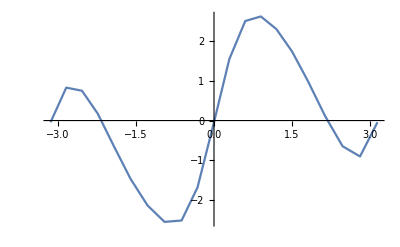
Crapboat | 
-Graphics3D- | 
Is it a boat? | Boatboat.
How big is it? | {9.5 cm,16.7 cm,3.3 cm}
Does it float? | True
How much is underwater? | 132.898 cm^2
Stability curve | -Graphics-
Does it float flat? | True
Trim Angle? | -49 °
What's the AVS? | {-180 °,-124 °,1 °,125 °,180 °}

```mathematica
boatboatboat[boat]
```